```mathematica
sol1=NDSolve[{D[u[t,x],t]+((t x)/(1+t^2)-1)D[u[t,x],x]+x D[u[t,x],x,x]==0,u[0,x]==x^2},u,{x,0,1},{t,0,0.03}]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolve::eerr: Warning: scaled local spatial error estimate of 479.547 at t = 0.03 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{u→InterpolatingFunction[{{0., 0.03}, {0., 1.}}, <>]}}

```mathematica
Plot3D[u[t,x]/.sol1,{t,0,0.03},{x,0,1},PlotRange->{All,All,{-1,5}}]
```

-Graphics3D-

```mathematica
{D[x^2/(1+(T-t)^2), t],D[x^2/(1+(T-t)^2), x],D[x^2/(1+(T-t)^2), x,x]}
```

{(2 (-t+T) x^2)/((1+(-t+T)^2)^2),(2 x)/(1+(-t+T)^2),2/(1+(-t+T)^2)}

```mathematica
FullSimplify[Reduce[(2 (-t+T) x^2)/((1+(-t+T)^2)^2)+a (2x)/(1+(T-t)^2)+b^2 2/(1+(T-t)^2)==0∧b>0,{a,b},Reals],{t≥ 0}]
```

√(x (-a+((t-T) x)/(1+(t-T)^2)))==b&&((x>0&&a<((t-T) x)/(1+(t-T)^2))||(a>((t-T) x)/(1+(t-T)^2)&&x<0))

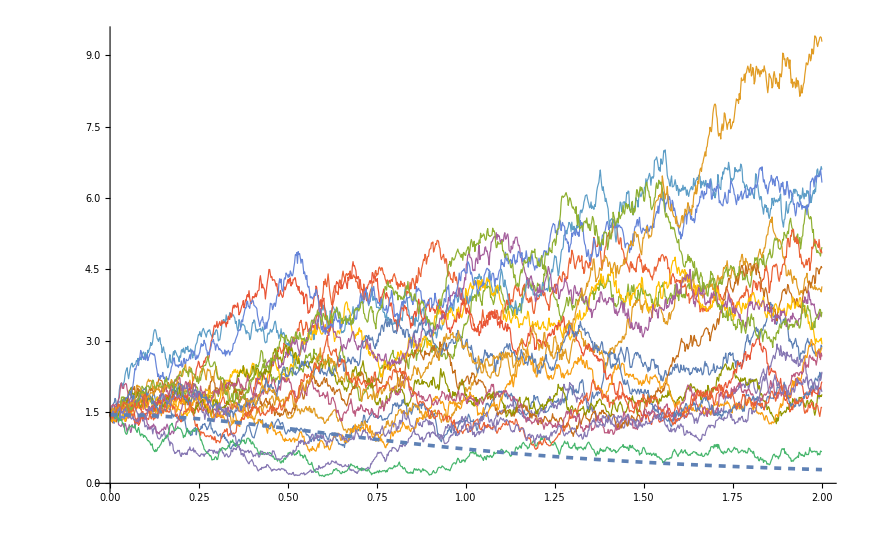

```mathematica
lines=Import["/home/stig/from windows/УЧЁБА!!!!!/4 курс/Диплом/coding/17.05.2016/sampleProcess/build-sampleProcess-Desktop-Debug/res_bad*.csv"];
Show[ListLinePlot[lines,PlotStyle->Thickness[0.001],PlotRange->All],Plot[(1.2)^2/(1+t^2),{t,0,2},PlotStyle->Directive[Dashed,Thickness[0.003]]]]
```